```mathematica
spring - damper system that takes moving average of sample times.
```

Note. We give the received time values the name ' xin' to avoid confusion with actual system time t. The filter ouptut is called 'x'.

There is noise on the wrap time found in the USB packets. The job here is to filter out the noise

### sample times. Each time is time wrap was reported. grep notifyWrap /var/log/system.log | awk ' // { print $7 "," }'

```mathematica
xin={76763275773239,76763415694627,76763554697344,76763693696303,76763833694256,76763972694507,76764111708459,76764251689290,76764390697055,76764529697793,76764669713269,76764808690299,76764947720532,76765087714626,76765226694422,76765365695326,76765505713111,76765644697375,76765783690332,76765922695217,76766062694079,76766201696413,76766340697642,76766480689488,76766619728540,76766758689674,76766898690324,76767037698374,76767176697208,76767316697965,76767455696709,76767594697427,76767734695221,76767873707171,76768012715046,76768152698518,76768291709114,76768430708418,76768570714824,76768709709122,76768848697051,76768988694168,76769127694659,76769266708503,76769406694451,76769545726319,76769684698385,76769824713581,76769963696814,76770102696850,76770242695407,76770381708669,76770520738785,76770659694732,76770799713008,76770938713420,76771077697480,76771217694211,76771356726038,76771495695266,76771635702566,76771774713933,76771913713548,76772053697567,76772192721330,76772331689678,76772471708576,76772610704985,76772749694557,76772889694718,76773028697079,76773167694255,76773307696820,76773446696662,76773585703695,76773725689843,76773864697076,76774003729091,76774143713836,76774282697991,76774421709692,76774561711327,76774700696972,76774839696377,76774979694326,76775118695270,76775257695891,76775397697359,76775536713477,76775675697216,76775815715579,76775954713205,76776093702757,76776233694643,76776372697487,76776511729356,76776651694265,76776790697154,76776929709208,76777068708498,76777208695790,76777347703539,76777486694597,76777626705652,76777765732278,76777904697309,76778044729539,76778183694864,76778322702549,76778462710044,76778601694226,76778740694110,76778880696795,76779019694504,76779158695353,76779298730690,76779437711152,76779576705013,76779716694656,76779855694677,76779994693923,76780134723091,76780273694976,76780412696806,76780552696723,76780691697446,76780830690137,76780970694262,76781109691144,76781248694711,76781388713093,76781527697298,76781666694368,76781806695068,76781945696935,76782084689825,76782224708757,76782363697044,76782502695796,76782642694669,76782781696826,76782920700446,76783060711226,76783199703295,76783338715203,76783477695213,76783617696783,76783756694990,76783895696735,76784035697663,76784174710078,76784313708932,76784453703770,76784592691481,76784731694912,76784871733929,76785010694817,76785149718055,76785289708168,76785428702701,76785567715607,76785707709663,76785846703567,76785985694311,76786125695043,76786264697977,76786403689823,76786543703326,76786682690055,76786821718980,76786961697331,76787100691674,76787239694534,76787379697028,76787518708478,76787657711132,76787797695872,76787936692157,76788075710592,76788215694397,76788354696916,76788493693503,76788633713246,76788772697546,76788911697162,76789051702444,76789190712770,76789329694840,76789468693922,76789608694357,76789747694380,76789886697249,76790026713473,76790165693137,76790304708810,76790444712880,76790583697776,76790722694207,76790862713058,76791001694902,76791140695107,76791280723676,76791419728489,76791558695348,76791698697484,76791837713788,76791976695115,76792116706709,76792255695057,76792394689960,76792534694889,76792673694517,76792812697043,76792952711351,76793091694949,76793230695530,76793370694367,76793509697569,76793648713261,76793788697491,76793927710766,76794066765476,76794206703132,76794345696984,76794484694320,76794624696360,76794763727176,76794902720353,76795042695343,76795181697537,76795320695005,76795460694661,76795599733814,76795738694326,76795877698330,76796017696782,76796156697831,76796295696349,76796435709801,76796574711790,76796713695947,76796853695807,76796992694608,76797131729925,76797271697424,76797410693366,76797549694579,76797689696836,76797828695129,76797967694582,76798107695292,76798246694434,76798385697353,76798525739295,76798664697139,76798803696685,76798943692315,76799082712559,76799221695251,76799361697345,76799500696387,76799639694459,76799779697353,76799918729574,76800057696424,76800197697588,76800336708188,76800475694331,76800615694764,76800754694937,76800893730810,76801033695113,76801172697305,76801311715242,76801451695208,76801590707165,76801729694394,76801869713548,76802008711764,76802147696917,76802286703531,76802426697165,76802565698193,76802704694136,76802844713626,76802983694445,76803122708504,76803262729090,76803401696942,76803540716348,76803680697134,76803819694833,76803958694620,76804098696521,76804237694146,76804376708667,76804516707153,76804655694250,76804794694596,76804934709618,76805073708701,76805212694743,76805352713390,76805491689529,76805630698188,76805770694287,76805909695471,76806048694726,76806188697410,76806327707575,76806466696912,76806606694473,76806745713382,76806884714959,76807024693808,76807163713340,76807302694643,76807442690652,76807581707798,76807720697032,76807860708766,76807999696317,76808138697020,76808277698008,76808417713385,76808556696667,76808695697170,76808835693680,76808974708483,76809113728906,76809253697064,76809392710802,76809531713880,76809671704681,76809810694697,76809949712354,76810089694614,76810228713670,76810367695658,76810507704672,76810646689922,76810785713650,76810925694969,76811064695868,76811203697526,76811343694413,76811482727186,76811621696772,76811761696914,76811900697110,76812039702953,76812179726024,76812318694651,76812457690429,76812597696117,76812736704840,76812875713321,76813015716353,76813154694474,76813293694300,76813433695696,76813572694214,76813711697496,76813851694819,76813990719073,76814129713461,76814269712945,76814408694894,76814547698770,76814686710462,76814826694239,76814965714425,76815104694632,76815244697412,76815383696793,76815522697059,76815662696659,76815801716526,76815940696491,76816080694153,76816219694263,76816358689428,76816498696972,76816637713100,76816776698247,76816916697150,76817055697087,76817194697288,76817334695042,76817473694838,76817612697512,76817752696556,76817891708821,76818030695724,76818170696990,76818309695216,76818448697338,76818588694429,76818727699129,76818866694766,76819006701547,76819145696632,76819284697054,76819424697291,76819563694890,76819702694771,76819842694191,76819981713157,76820120696349,76820260730153,76820399697213,76820538716208,76820678712415,76820817694328,76820956697333,76821095689939,76821235697516,76821374696961,76821513734140,76821653710263,76821792694312,76821931695406,76822071694243,76822210690980,76822349694856,76822489694670,76822628694732,76822767697689,76822907694305,76823046696979,76823185715328,76823325694545,76823464713761,76823603694006,76823743695104,76823882744180,76824021697438,76824161696692,76824300713412,76824439713168,76824579693951,76824718694043,76824857695419,76824997689920,76825136694152,76825275705101,76825415696386,76825554693296,76825693692916,76825833694768,76825972693154,76826111706350,76826251695261,76826390697768,76826529694579,76826669751276,76826808694660,76826947694727,76827086694155,76827226713038,76827365710631,76827504705870,76827644694958,76827783696717,76827922694948,76828062694045,76828201708805,76828340693909,76828480697409,76828619696979,76828758703219,76828898713359,76829037694542,76829176697655,76829316693912,76829455697306,76829594694780,76829734694029,76829873715071,76830012697817,76830152706172,76830291696832,76830430714900,76830570693936,76830709693330,76830848694208,76830988692512,76831127728722,76831266708615,76831406697116,76831545697213,76831684696425,76831824694642,76831963709122,76832102694208,76832242703608,76832381696553,76832520694704,76832660694856,76832799713044,76832938712965,76833078694802,76833217694880,76833356728910,76833495706630,76833635697064,76833774703009,76833913696493,76834053731029,76834192695383,76834331695728,76834471734347,76834610694787,76834749697059,76834889694337,76835028694973,76835167722415,76835307695099,76835446695114,76835585694795,76835725698449,76835864697533,76836003707327,76836143696954,76836282697171,76836421713650,76836561690097,76836700696562,76836839693500,76836979713759,76837118724815,76837257697394,76837397713442,76837536710826,76837675712462,76837815696248,76837954697560,76838093695252,76838233733304,76838372727973,76838511708269,76838651713677,76838790698023,76838929697047,76839069694860,76839208694807,76839347708998,76839486718997,76839626708978,76839765695633,76839904691747,76840044702267,76840183710412,76840322694536,76840462728922,76840601695112,76840740708615,76840880730189,76841019729353,76841158694853,76841298703405,76841437705493,76841576693845,76841716698006,76841855729540,76841994695010,76842134713770,76842273729573,76842412694698,76842552703575,76842691732146,76842830694359,76842970719200,76843109729715,76843248730561,76843388709086,76843527700200,76843666696578,76843806713268,76843945713545,76844084689494,76844224696878,76844363713693,76844502690467,76844642697663,76844781696983,76844920708282,76845060699090,76845199708973,76845338694178,76845478706480,76845617695264,76845756716498,76845895698937,76846035720061,76846174697466,76846313694525,76846453697793,76846592694723,76846731696628,76846871713518,76847010694771,76847149708779,76847289714087,76847428694790,76847567695108,76847707695040,76847846694710,76847985697114,76848125729848,76848264694027,76848403707806,76848543697745,76848682712766,76848821695347,76848961696971,76849100693893,76849239694014,76849379713192,76849518709305,76849657697463,76849797697083,76849936697535,76850075694859,76850215694330,76850354690207,76850493701006,76850633713578,76850772709388,76850911697353,76851051697233,76851190697190,76851329694669,76851469709355,76851608695359,76851747696618,76851887697671,76852026694049,76852165715345,76852304694300,76852444695016,76852583694479,76852722708599,76852862695187,76853001706636,76853140697060,76853280714218,76853419696902,76853558694007,76853698723135,76853837694407,76853976699713,76854116703516,76854255694346,76854394710080,76854534697266,76854673712944,76854812697154,76854952713733,76855091694434,76855230709900,76855370708434,76855509696238,76855648730855,76855788708860,76855927694463,76856066713034,76856206694296,76856345696931,76856484709677,76856624694704,76856763729624,76856902694544,76857042697236,76857181696491,76857320695513,76857460709088,76857599694807,76857738713149,76857878690366,76858017695192,76858156694027,76858295725277,76858435713440,76858574697189,76858713707568,76858853695550,76858992713470,76859131694991,76859271728382,76859410694326,76859549692446,76859689708212,76859828696362,76859967732221,76860107702493,76860246696977,76860385694335,76860525720819,76860664729380,76860803694760,76860943694486,76861082695045,76861221695641,76861361695388,76861500711505,76861639694156,76861779713808,76861918729160,76862057694230,76862197698190,76862336713517,76862475694716,76862615694734,76862754702409,76862893694240,76863033712906,76863172694244,76863311694900,76863451714417,76863590706811,76863729712080,76863869693935,76864008713519,76864147694642,76864287694437,76864426689983,76864565729481,76864704694707,76864844694561,76864983694344,76865122708899,76865262696806,76865401696768,76865540694378,76865680694162,76865819698552,76865958693840,76866098705759,76866237713222,76866376696465,76866516697313,76866655697013,76866794710215,76866934694680,76867073713454,76867212697619,76867352713156,76867491694823,76867630697332,76867770737245,76867909695538,76868048696979,76868188694241,76868327697007,76868466704585,76868606696207,76868745723897,76868884709113,76869024713309,76869163696908,76869302697130,76869442694201,76869581696124,76869720708389,76869860714549,76869999722813,76870138696851,76870278695323,76870417697065,76870556694130,76870695694555,76870835696265,76870974711045,76871113697435,76871253698709,76871392696385,76871531697549,76871671694903,76871810715345,76871949694638,76872089714913,76872228695148,76872367694803,76872507713618,76872646697979,76872785712959,76872925694500,76873064694692,76873203694896,76873343695026,76873482715990,76873621725710,76873761695777,76873900697297,76874039696371,76874179690104,76874318694627,76874457702699,76874597697773,76874736703743,76874875729795,76875015703179,76875154694830,76875293718893,76875433694445,76875572694658,76875711694376,76875851694719,76875990713386,76876129713713,76876269713618,76876408697527,76876547725553,76876687707607,76876826691802,76876965695451,76877104697523,76877244696356,76877383703103,76877522696569,76877662705586,76877801697719,76877940694202,76878080694669,76878219713353,76878358695363,76878498708905,76878637696889,76878776729350,76878916709005,76879055697719,76879194694186,76879334713533,76879473694522,76879612694301,76879752715225,76879891698198,76880030694560,76880170688616,76880309696402,76880448694896,76880588713237,76880727713664,76880866708905,76881006709948,76881145696383,76881284712917,76881424694185,76881563697093,76881702695232,76881842713578,76881981713364,76882120694493,76882260706412,76882399714389,76882538728769,76882678709232,76882817702586,76882956733193,76883095698868,76883235709281,76883374694878,76883513690113,76883653714830,76883792697286,76883931708739,76884071713065,76884210745228,76884349702614,76884489712842,76884628702896,76884767794427};
```

```mathematica
xin=Drop[xin,-20]; (*end is always a mess *)
```

88.2 kHz
inputSize= 538 multFactor= 6
new bufferSize = 73728 numSamplesInBuffer = 12288

```mathematica
bufsize=12288;
```

```mathematica
rate=88200;
```

#### Expected time between wraps in ns

```mathematica
Texpected=10^9 bufsize /rate//N
```

1.3932×10^8

## CHECK We may want to skip the first frames is this is happening consistently

#### If we start at the wrong moment, where the timing is off from the main pulse, the filter has to adjust to get into the beat. Apparently the first beats are off the main beat. This makes huge difference in max error/drift after fitlering.

```mathematica
xin=Drop[xin,5]; (* test. There seems a hickup in sample 3 *)
```

```mathematica
deltas=10^-6(Drop[xin,1]-Drop[xin,-1]);
```

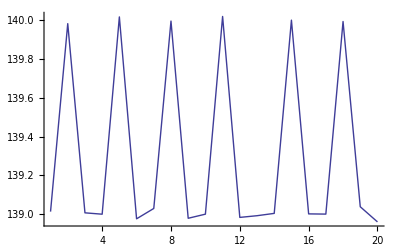

```mathematica
ListPlot[Take[deltas,20],PlotJoined->True,PlotRange->All]
```

```mathematica
(*xin=Take[xin,{200,220}]; (*testing *)
```

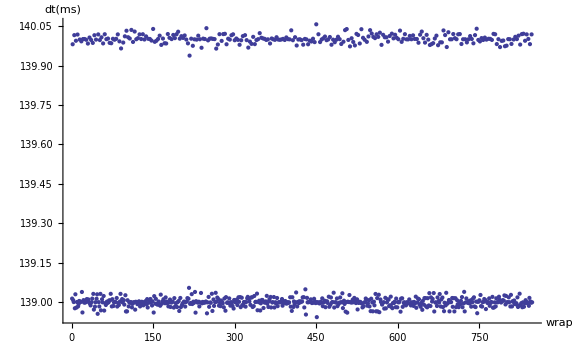

```mathematica
ListPlot[deltas, AxesLabel->{"wrap","dt(ms)"},PlotRange->All]
```

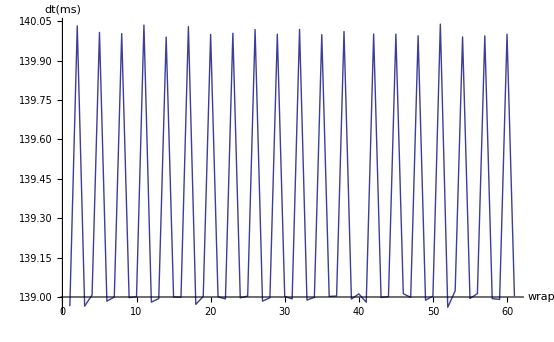

```mathematica
ListPlot[Take[deltas,{100,160}], AxesLabel->{"wrap","dt(ms)"},PlotRange->All,PlotJoined->True]
```

```mathematica
Mean[10^-6(Drop[xin,1]-Drop[xin,-1])]//N
```

139.326

#### Init the filter with first sample

```mathematica
x0=xin[[1]]
```

76763972694507

```mathematica
xin=Drop[xin,1]; (* first element was used so do not reuse *)
```

```mathematica
x=x0; (* filtered x *)
u=0; (* u = x-xin : the 'error' is the spring extension *)
dx=Texpected; (* dx/dt = expected change rate of filtered x *)
```

```mathematica
xin[[1]]-x
```

139013952

#### Spring constant

```mathematica
K=1;
```

Damping constant

The mass, this determines how slow system follows changes in xin. Bigger=slower.

```mathematica
M=10000;
```

```mathematica
Da=2 √(M K); (*cricital damping *)
```

## Filter

#### Simple filter. This does work in the right direction but lacks damping so lot of overshoot.

```mathematica
filter[inputx_]:=Module[{},
xnext=x+dx;
du=inputx-x;
dx=(99dx+du)/100; (*exponential towards target *)
x=xnext;
x
]
```

#### spring - damper based filter. Is jumpy.

```mathematica
filter[inputx_]:=Module[{},(*{F,du,xnext,unext},*)
xnext=x+dx ;(* the next filtered output *)
unext=inputx-xnext; (*error u *)

du = unext-u; (* change of the error, for damping *)
F=K unext + Da du; (* force on spring *)
dx = dx + F/M ; 

x=xnext; u=unext; (* update the filter *)
x
];
```

#### spring - damper filter with outlier check/skip

Works great for the test set. Only worry is that the jitter detect uses the du which is change of error.
  An absolute distance of unext from Texpected might be better but in practice it seems worse

```mathematica
filter[inputx_]:=Module[{xnext, unext, du, F},(*{F,du,xnext,unext},*)
xnext=x+dx ;(* the next filtered output *)
unext=inputx-xnext; (*error u *)

du = unext-u; (* change of the error, for damping *)
F=K unext + Da du; (* force on spring *)
dx = dx + F/M ;
x=xnext; u=unext; (* update the filter *)
x
];
```

```mathematica
xfiltered = filter/@xin;
```

```mathematica
10^-6(xfiltered-xin)[[4]]
```

0.27757

### Does it follow xin?

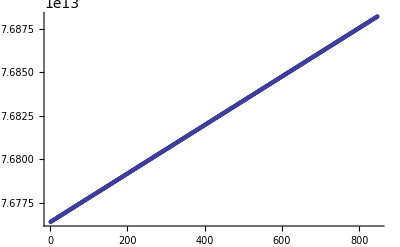

```mathematica
ListPlot[xfiltered]
```

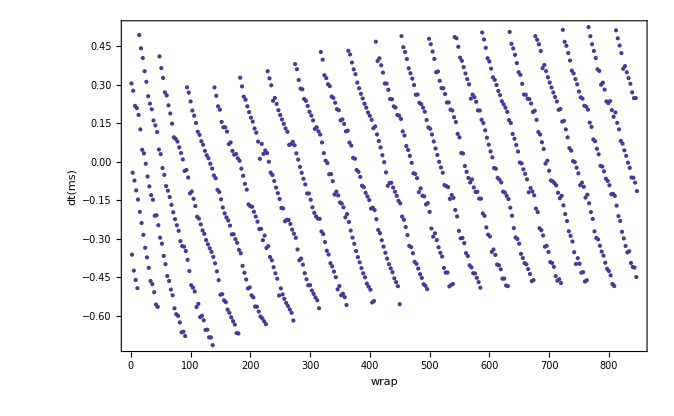

```mathematica
ListPlot[10^-6(xfiltered-xin), FrameLabel->{"wrap","dt(ms)"},PlotRange->All,Frame->True]
```

So the data can come in up to 6 ms late. This is the timestamps straight coming from USB

### Does it keep a solid rate without jumping?

```mathematica
deltas=(Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected;
```

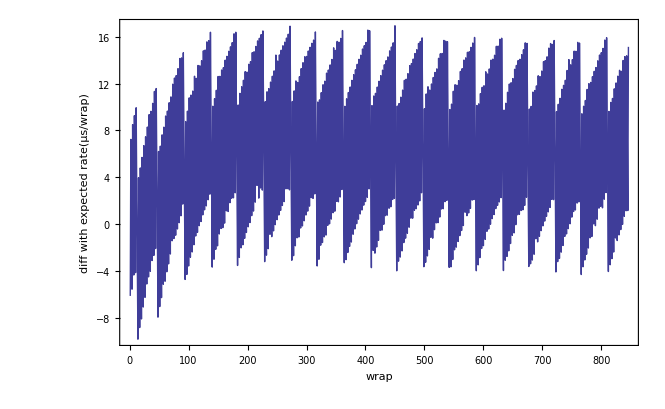

```mathematica
ListPlot[10^-3((Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected), FrameLabel->{"wrap","diff with expected rate(μs/wrap)"},Frame->True,PlotJoined->True]
```

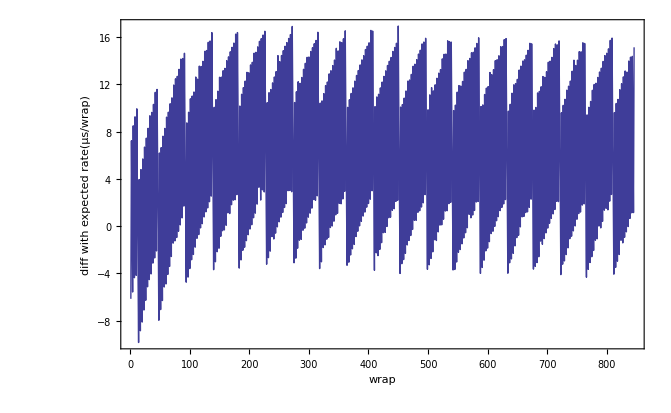

```mathematica
ListPlot[10^-3((Drop[xfiltered,1]-Drop[xfiltered,-1])-Texpected), FrameLabel->{"wrap","diff with expected rate(μs/wrap)"},Frame->True,PlotJoined->True,PlotRange->All]
```